# Aula de Mapeamento Geométrico março de 2014

## Elementos Finitos: Metodologia de aproximação numérica que envolve a integral de uma função sobre o domínio estudado.

Analogia simples : Movimento variado (não uniforme)

Fornecida a equação da posição em função do tempo:

```mathematica
CONSTANTE=20;
s[t_]:=CONSTANTE+5 t-10 t^2+3 t^3;
sgr=Plot[s[t],{t,0,3},AxesOrigin->{0,0},Filling->Axis]
```

-Graphics-

Obtenção da equação da velocidade instantânea: v = ds/dt

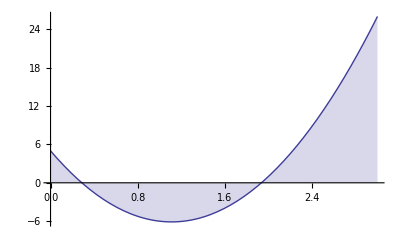

```mathematica
v[t_]:=(D[s[time],time])/.time->t;
vgr=Plot[v[t],{t,0,3},AxesOrigin->{0,0},Filling->Axis]
```

Fornecida equação da velocidade instantânea:

```mathematica
Velocidade=v[t]
```

5-20 t+9 t^2

Obtenção da equação da posição: s =∫vⅆt

```mathematica
Posicao=(∫_0^t Velocidadeⅆt)+CONSTANTE
```

20+5 t-10 t^2+3 t^3

Em elementos finitos, o que normalmente se tem é a equação análoga à da velocidade instantânea cuja solução é a equação da posição, mas sem integral analítica de fácil dedução.

## Integração Numérica: Algoritmos que estimam o valor numérico da integral definida sobre um domínio.

Exemplo: deseja-se a posiçãoo no intante t = 2 u.t. (unidades de tempo)

```mathematica
tt=2.5;
Ninterval=30;
```

```mathematica
posicao2utANALITICA=Posicao/.t->tt
```

16.875

Regra dos Retângulos:

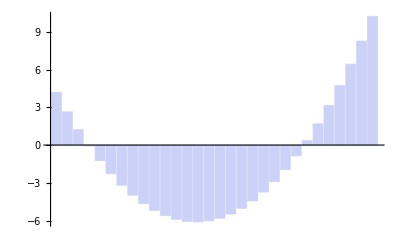

16.862

```mathematica
ptsRet[t_,Nintervalos_]:=Table[v[t/(2 Nintervalos)+(p-1)*t/Nintervalos],{p,1,Nintervalos}];
BarChart[ptsRet[tt,Ninterval]]
integralRetang[t_,Nintervalos_]:=N[∑_(p=1)^Nintervalos (v[t/(2 Nintervalos)+(p-1)*t/Nintervalos]*t/Nintervalos)+CONSTANTE];

integralRetang[tt,Ninterval]
```

Regra dos Trapézios:

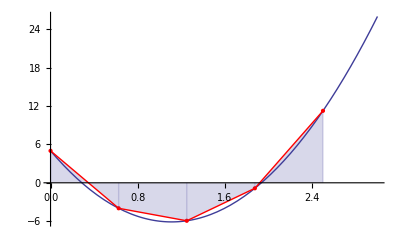

18.0225

```mathematica
Ninterval=4;
ptsTrap[t_,Nintervalos_]:=Table[{(p)*t/Nintervalos,v[(p)*t/Nintervalos]},{p,0,Nintervalos}];
Show[{Plot[v[t],{t,0,3}],ListPlot[ptsTrap[tt,Ninterval],Joined->False,PlotRange->All,Filling->Axis,PlotStyle->Red],ListPlot[ptsTrap[tt,Ninterval],Joined->True,PlotRange->All,Filling->Axis,PlotStyle->Red]}]

integralTrap[t_,Nintervalos_]:=N[∑_(p=1)^(Nintervalos-1) ((v[(p)*t/Nintervalos]+v[(p+1)*t/Nintervalos])/2*t/Nintervalos)+CONSTANTE];
integralTrap[tt,Ninterval]
```

Quadratura de Gauss:

-Graphics-

```mathematica
ptp3[t_]:={(-√(3/5)+1)t/2,(0+1)t/2,(+√(3/5)+1)t/2};
wp3={5/9,8/9,5/9};

integralQuadGauss[t_]:=N[(wp3[[1]]*v[ptp3[t][[1]]]+wp3[[2]]*v[ptp3[t][[2]]]+wp3[[3]]*v[ptp3[t][[3]]])*tt/2]+CONSTANTE
integralQuadGauss[tt]
```

16.875

## Equivalência de Integral sobre Domínio Mapeado:

-Graphics-

```mathematica
IntegralDominioVerdadeiro=N[∫_0^tt v[t]ⅆt+CONSTANTE]
```

16.875

```mathematica
g[t_,ξ_]:=t(ξ+1)/2; (* FUNÇÃO MAPEAMENTO   -1 ≤ ξ ≤ +1    *)
```

```mathematica
g[tt,-1]
```

0.

```mathematica
g[tt,1]
```

2.5

```mathematica
JacG={{D[g[tt,ξ],ξ]}} (* MATRIZ JACOBIANA DA FUNÇÃO MAPEAMENTO *)
```

{{1.25}}

```mathematica
detJacG=Det[JacG] (* DETERMINANTE DA MATRIZ JACOBIANA DA FUNÇÃO MAPEAMENTO *)
```

1.25

```mathematica
IntegralDominioReferencia=∫_-1^1 v[g[tt,ξ]]*detJacGⅆξ+CONSTANTE//N
```

16.875

```mathematica
IntegralDominioVerdadeiro-IntegralDominioReferencia
```

0.

## Funções de Forma:

Linha:

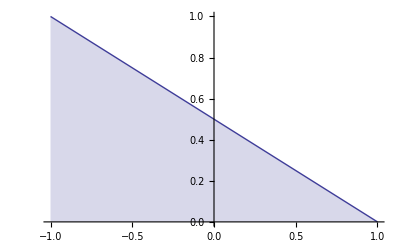

```mathematica
φ0Linha[ξ_]:=(1-ξ)/2;
Plot[φ0Linha[ξ],{ξ,-1,1},Filling->Axis]
```

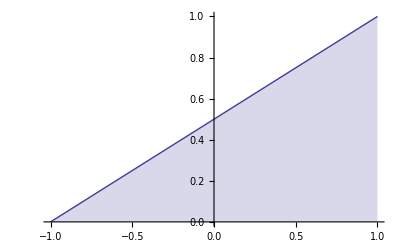

```mathematica
φ1Linha[ξ_]:=(1+ξ)/2;
Plot[φ1Linha[ξ],{ξ,-1,1},Filling->Axis]
```

```mathematica
Xline[ξ_,n0_,n1_]:=n0*φ0Linha[ξ]+n1*φ1Linha[ξ];

node0L={3,2,5};
node1L={7,1,1};
grline=ParametricPlot3D[Xline[ξ,node0L,node1L],{ξ,-1,1},PlotRange->{{0,10},{0,10},{0,10}}];
Manipulate[Show[{grline,Graphics3D[Sphere[Xline[ξ,node0L,node1L],0.2]]}],{ξ,-1,1,0.2}]
```

Quadrilátero:

```mathematica
φ0Quadrilatero[ξ_,η_]:=(1-ξ)/2(1-η)/2;
Plot3D[φ0Quadrilatero[ξ,η],{ξ,-1,1},{η,-1,1},Filling->Axis]
```

-Graphics3D-

```mathematica
φ1Quadrilatero[ξ_,η_]:=(1+ξ)/2(1-η)/2;
Plot3D[φ1Quadrilatero[ξ,η],{ξ,-1,1},{η,-1,1},Filling->Axis]
```

-Graphics3D-

```mathematica
φ2Quadrilatero[ξ_,η_]:=(1+ξ)/2(1+η)/2;
Plot3D[φ2Quadrilatero[ξ,η],{ξ,-1,1},{η,-1,1},Filling->Axis]
```

-Graphics3D-

```mathematica
φ3Quadrilatero[ξ_,η_]:=(1-ξ)/2(1+η)/2;
Plot3D[φ3Quadrilatero[ξ,η],{ξ,-1,1},{η,-1,1},Filling->Axis]
```

-Graphics3D-

```mathematica
Xquadrilatero[ξ_,η_,n0_,n1_,n2_,n3_]:=n0*φ0Quadrilatero[ξ,η]+n1*φ1Quadrilatero[ξ,η]+n2*φ2Quadrilatero[ξ,η]+n3*φ3Quadrilatero[ξ,η];

node0Q={3,2,3};
node1Q={7,1,4};
node2Q={8,6,2};
node3Q={4,4,6};
grquadrilatero=ParametricPlot3D[Xquadrilatero[ξ,η,node0Q,node1Q,node2Q,node3Q],{ξ,-1,1},{η,-1,1},PlotRange->{{3,8},{1,6},{1,6}}];
Manipulate[Show[{grquadrilatero,Graphics3D[Sphere[Xquadrilatero[ξ,η,node0Q,node1Q,node2Q,node3Q],0.1]]}],{ξ,-1,1,0.2},{η,-1,1,0.2}]
```

Exemplo deste Mapeamento (Quadrilátero) no PZ:

```mathematica
Xquadrilatero[0.23,-0.17,node0Q,node1Q,node2Q,node3Q]
Xquadrilatero[-0.89,0.31,node0Q,node1Q,node2Q,node3Q]
Xquadrilatero[0.05,1,node0Q,node1Q,node2Q,node3Q]
Xquadrilatero[-0.73,-0.35,node0Q,node1Q,node2Q,node3Q]
```

{5.875,2.98067,3.58388}

{3.875,3.36308,4.83988}

{6.1,5.05,3.9}

{3.865,2.64663,3.89063}

## Matriz Jacobiana do Mapeamento Linear do Quadrilatero:

```mathematica
funcMapQuad=Xquadrilatero[ξ,η,node0Q,node1Q,node2Q,node3Q]
```

{3/4 (1-η) (1-ξ)+(1+η) (1-ξ)+7/4 (1-η) (1+ξ)+2 (1+η) (1+ξ),1/2 (1-η) (1-ξ)+(1+η) (1-ξ)+1/4 (1-η) (1+ξ)+3/2 (1+η) (1+ξ),3/4 (1-η) (1-ξ)+3/2 (1+η) (1-ξ)+(1-η) (1+ξ)+1/2 (1+η) (1+ξ)}

```mathematica
DxDξ=D[funcMapQuad[[1]],ξ];
DxDη=D[funcMapQuad[[1]],η];

DyDξ=D[funcMapQuad[[2]],ξ];
DyDη=D[funcMapQuad[[2]],η];

DzDξ=D[funcMapQuad[[3]],ξ];
DzDη=D[funcMapQuad[[3]],η];
```

```mathematica
Jac=({{DxDξ, DxDη}, {DyDξ, DyDη}, {DzDξ, DzDη}});
```

```mathematica
Jac//MatrixForm
```

(-2 η+2 (1+η) | 1-(3 (1-ξ))/4-ξ+(1+ξ)/4
-1+(1-η)/4+1/2 (-1+η)-η+(3 (1+η))/2 | 1+1/4 (-1-ξ)+1/2 (-1+ξ)-ξ+(3 (1+ξ))/2
-3/4 (1-η)-2 η | -1+(3 (1-ξ))/4-ξ+(1+ξ)/2)

```mathematica
AxesPZ[qsi_,eta_]:=N[Orthogonalize[Jac/.{ξ->qsi,η->eta}]];
JacPZ[qsi_,eta_]:=Transpose[AxesPZ[qsi,eta]].(Jac/.{ξ->qsi,η->eta})
```

```mathematica
AxesPZ[-1,-1]
```

{{0.970143,0.242536},{-0.242536,0.970143},{0.,0.}}

```mathematica
JacPZ[-1,-1]
```

{{2.06155,0.242536},{0.,1.09141}}

```mathematica
DetPZ[qsi_,eta_]:=Det[JacPZ[qsi,eta]];
```

```mathematica
DetPZ[-1,-1]
```

2.25